```mathematica
Quit[]
```

```mathematica
"Units:"
"Time: years"
"Length: pc"
"Mass: Solar mass"
a:=20000(*20 000 pc = 20kpc*)
M:=10^12(*Solar masses*)
m:=4*10^6(*Solar masses*)
G:=4.49*10^-15(*pc^3/(solar mass * yr^2)*)
c:=0.3064(*pc/yr*)
Subscript[m, p]:=10^-3(*Solar mass *)
Rs:=2(G m)/c^2
```

Units:

Time: years

Length: pc

Mass: Solar mass

```mathematica
Quit[]
```

```mathematica
"Schwarzschild radial velocity"
fourVelocity[Ε_,L_]=√(Ε^2/(Subscript[m, p]^2 c^2)-(1-Rs/r)(c^2+h^2/r^2))/.{r->1/u,h->L/Subscript[m, p]}//FullSimplify
```

Schwarzschild radial velocity

√(-0.093881+u (3.592×10^-8+L^2 (-1.×10^6+0.382612 u) u)+1.06518×10^7 Ε^2)

```mathematica
"Roots, see the limits file in this dir"
u1[Ε_,L_]:=Root[(c^2 L^2)/Ε^2-(c^2 L^2 Rs #1)/Ε^2-L^2/(c^2 Subscript[m, p]^2)+(L^4 #1^2)/(Ε^2 Subscript[m, p]^2)-(L^4 Rs #1^3)/(Ε^2 Subscript[m, p]^2)&,1]
u2[Ε_,L_]:=Root[(c^2 L^2)/Ε^2-(c^2 L^2 Rs #1)/Ε^2-L^2/(c^2 Subscript[m, p]^2)+(L^4 #1^2)/(Ε^2 Subscript[m, p]^2)-(L^4 Rs #1^3)/(Ε^2 Subscript[m, p]^2)&,2]
u3[Ε_,L_]:=Root[(c^2 L^2)/Ε^2-(c^2 L^2 Rs #1)/Ε^2-L^2/(c^2 Subscript[m, p]^2)+(L^4 #1^2)/(Ε^2 Subscript[m, p]^2)-(L^4 Rs #1^3)/(Ε^2 Subscript[m, p]^2)&,3]
```

Roots, see the limits file in this dir

```mathematica
"Schwarzschild Radial action"
radialAction[Ε_,L_]:=NIntegrate[fourVelocity[Ε,L],{u,u1[Ε,L],u2[Ε,L]}]
```

Schwarzschild Radial action

Plot values:

0.000765224

-0.000112629

1.55526×10^-7

833.041+2.36155×10^-23 ⅈ

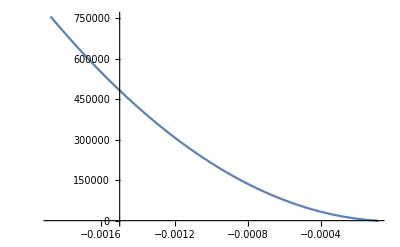

```mathematica
"Plot values:"
r=2000Rs
Ε=-√((c^4 r Subscript[m, p]^2-c^4 Rs Subscript[m, p]^2)/r)*1.2
Lmax=√((r^3 Ε^2-c^4 r^3 Subscript[m, p]^2+c^4 r^2 Rs Subscript[m, p]^2)/(c^2 r Subscript[m, p]^2-c^2 Rs Subscript[m, p]^2))Subscript[m, p]
radialAction[Ε,Lmax*0.5]
Plot[Re[radialAction[Ε,Lmax*0.5]],{Ε,-√((c^4 r Subscript[m, p]^2-c^4 Rs Subscript[m, p]^2)/r),-√((c^4 r Subscript[m, p]^2-c^4 Rs Subscript[m, p]^2)/r)*20}]
```